```mathematica
SetDirectory["C:/MessdatenEingang"];
Dateien=FileNames[];
Framed[ListPicker[Dynamic[px],Dateien],FrameStyle->Green,RoundingRadius->10]
```

$CellContext`px

```mathematica
filename=px;
OrdnerInhalt=FileNames["*",filename];
SetDirectory["C:/MessdatenEingang/"<>filename];
textDateien =FileNames["*.txt"] ;
gelDatei=Import[textDateien[[1]], "Data"] ; (* Importiere die .txtDatei  *)
Manipulate[gelDatei[[i]],{i,0,22,1}] (* Manipulate über die Zeilenm*)
(* Nehme die Zeilen mit Informationen über die Probe *)
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= Quantity[gelDatei[[8]][[2]],"s"];
ProbenName = ToString[gelDatei[[4]][[2]]];
Temp = Quantity[gelDatei[[7]][[2]],"Kelvin"];
ExcPow= Quantity[gelDatei[[20]][[2]],"kilowatt per cm^2"];
```

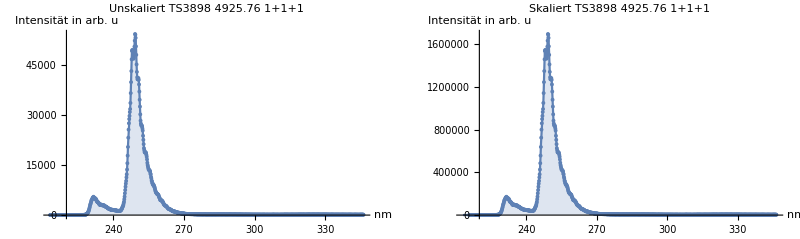
{{Null^8 -Graphics-,□}}

```mathematica
{{f = Interpolation[gelDatei[[21;; All]],InterpolationOrder->1];
skalFaktor= QuantityMagnitude[1/IntegZeit];
gelDateiSkal= gelDatei[[21 ;;All]];
gelDateiSkal[[All,2]]=gelDateiSkal[[All,2]] * skalFaktor;
(*Integrate[f,{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*)
integInt=Integrate[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*skalFaktor;
PlotTitel= ProbenName<> " " <>ToString[QuantityMagnitude[ExcPow]] <> " " <> ToString[FilterKombo];

p1 = Show[Plot[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]} , Filling->Axis,PlotRange->Full, Axes-> True,AxesLabel->{" nm","Intensität in arb. u"},
PlotLabel->"Unskaliert"<> " " <> PlotTitel],ListPlot[gelDatei[[21;; All]], Axes->True,PlotRange-> Automatic]];
p2= Show[Plot[f[x]*skalFaktor,{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]} , Filling->Axis,PlotRange->Full, Axes-> True,AxesLabel->{" nm","Intensität in arb. u"},
PlotLabel->"Skaliert"<> " " <> PlotTitel],ListPlot[gelDateiSkal[[21;; All]], Axes->True,PlotRange-> Automatic]];
GraphicsGrid[{{p1,p2}},ImageSize-> 800], □}}
```

```mathematica
dataset=Dataset[{
<|"FilterKombo"->FilterKombo,"Temp"->QuantityMagnitude[Temp],"Integrationszeit"->IntegZeit,"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> ExcPow,"Datenpunkte"-> gelDateiSkal[[1 ;;All]]|>}]
```

```mathematica
filename=px;
OrdnerInhalt=FileNames["*",filename];
SetDirectory["C:/MessdatenEingang/"<>filename];
textDateien =FileNames["*.txt"] ;
gelDatei=Import[textDateien[[1]], "Data"] ; (* Importiere die .txtDatei  *)
(* Nehme die Zeilen mit Informationen über die Probe *)
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= gelDatei[[8]][[2]];
ProbenName = ToString[gelDatei[[4]][[2]]];
Temp = gelDatei[[7]][[2]];
ExcPow=gelDatei[[20]][[2]];
datasetTest=Dataset[{
<|"FilterKombo"->FilterKombo,"Temp"->Temp,"Integrationszeit"->IntegZeit,"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> ExcPow,"Integrierte Int."->integInt|>}];
SetSharedVariable[datasetTest]
```

```mathematica
ParallelDo[
gelDatei=Import[textDateien[[i]], "Data"];
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= gelDatei[[8]][[2]];
ProbenName =gelDatei[[4]][[2]];
Temp =gelDatei[[7]][[2]];
ExcPow= gelDatei[[20]][[2]];
skalFaktor= 1/IntegZeit;
f = Interpolation[gelDatei[[21;; All]],InterpolationOrder->1];
gelDateiSkal= gelDatei[[21 ;;All]];
gelDateiSkal[[All,2]] * skalFaktor;
integInt=Integrate[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*skalFaktor;
datasetTest =AppendTo[datasetTest,<|"FilterKombo"->FilterKombo,"Temp"->Temp,"Integrationszeit"->IntegZeit,"ProbenName"->ProbenName,"Anregungsleistungsdichte"->ExcPow,"Integrierte Int."->integInt|>];,{i,2,textDateien//Length,1}];
```

```mathematica
datasetTestNamen= datasetTest[All,"ProbenName"];
datasetTestNamen=DeleteDuplicates[datasetTestNamen];

probe =datasetTestNamen[[1]]
```

TS3898

```mathematica
datasetTest=datasetTest[Select[#Temp == 300&]];
```

```mathematica
datasetTestInt=datasetTest[All,{"ProbenName","Integrierte Int.","Anregungsleistungsdichte"}];
datasetTestAnr = datasetTest[All,{"ProbenName","Integrierte Int.","Anregungsleistungsdichte"}];
datasetTestInt = datasetTestInt[GroupBy["ProbenName"], Catenate,{"Integrierte Int."}];
datasetTestAnr = datasetTestAnr[GroupBy["ProbenName"], Catenate,{"Anregungsleistungsdichte"}];
```

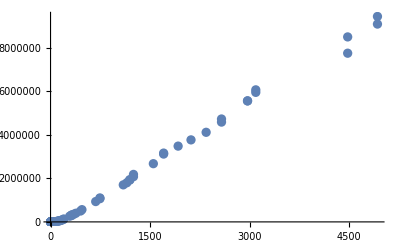
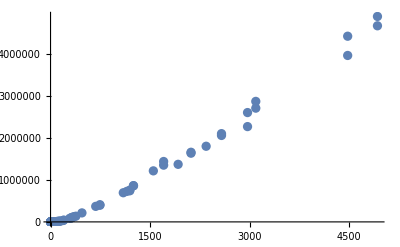
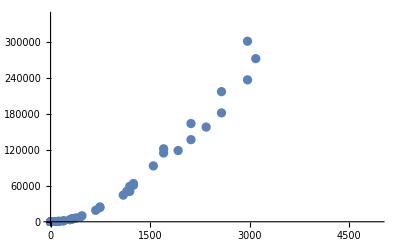
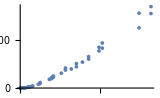

```mathematica
ParallelTable[
xaxis=Normal[datasetTestAnr[i]];
yaxis =Normal[datasetTestInt[i]];
Liste=ConstantArray[1,{xaxis//Length,2}];
Liste[[;;,2]] = yaxis;
Liste[[;;,1]] =xaxis;
ListPlot[Liste],{i,1,datasetTestNamen//Length,1}]
```